# Mean absorption probability of a purely absorbing spherical particle

## References

Duysens 1956 = The flattening of the absorption spectrum of suspensions, as compared to that of solutions

Van de Hulst 1957 - Light scattering by small particles

Morel and Bricaud 1981 - Theoretical results concerning light absorption in a discrete medium, and application to specific absorption of phytoplankton

## Exact result

Mean absorption probability Qa for a uniform ray that strikes a sphere of radius r with absorption coefficient σ:

```mathematica
Qa[σ_,r_]:=1-(ⅇ^(-2 r σ) (-1+ⅇ^(2 r σ)-2 r σ))/(2 r^2 σ^2)
```

## Derivation

Integrate over two random numbers x1 and x2 in [0,1] that randomly sample a disk, project onto the sphere, and compute the resulting Beer calculation:

```mathematica
Integrate[Exp[-σ 2 √(1-#.#)]&[√x1{Cos[2 Pi x2],Sin[2 Pi x2]}],{x1,0,1},{x2,0,1}]
```

(ⅇ^(-2 σ) (-1+ⅇ^(2 σ)-2 σ))/(2 σ^2)

## Monte Carlo validation

```mathematica
DiskSample[]:=√RandomReal[]{Sin[#],Cos[#]}&[RandomReal[{0,2Pi}]]
```

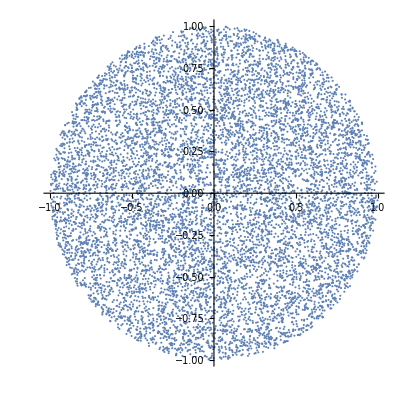

```mathematica
ListPlot[Table[DiskSample[],{i,Range[10000]}],AspectRatio->1]
```

```mathematica
With[{σ=.5},
{
Mean[Table[Exp[-2σ √(1-#.#)]&[DiskSample[]],{i,Range[100000]}]],
(ⅇ^(-2 σ) (-1+ⅇ^(2 σ)-2 σ))/(2 σ^2)
}
]
```

{0.528215,0.528482}